```mathematica
Clear["Global`*"]
```

```mathematica
pump = 1.1;
```

```mathematica
(*gating variable*)
am=0.32*(54+v)/(1-Exp[(-(v+54)/4)]);
bm=0.28*(v+27)/(Exp[((v+27)/5)]-1);
ah=0.128*Exp[-(50+v)/18];
bh=4/(1+Exp[(-(v+27)/5)]);
an=0.032*(v+52)/(1-Exp[(-(v+52)/5)]);
bn=0.5*Exp[(-(v+57)/40)];
meq= am/(am+bm);
heq= ah/(ah+bh);
neq= an/(an+bn);
```

```mathematica
(*concentrations*)
NKo=1.16058867964936*10^-15;
NKi=2.01327337006624*10^-13;
NNao=2.83145226320044*10^-14;
NNai=2.71049059394185*10^-14;
NClo=2.52662545231757*10^-14;
NCli=1.00379740482485*10^-14;
Voli=1.44424294570548*10^-15;
O2=28.9175980624225;
Ko=NKo/Volo;
Ki=NKi/Voli;
Nao=NNao/Volo;
Nai=NNai/Voli;
Clo=NClo/Volo;
Cli=NCli/Voli;
```

```mathematica
(*parameters*)
GK=25;GNa=30;
glcl=0.1;glk=0.05;glna=0.0247*1.5;c=1.0;dslp=0.25;gmag=5;
sigma=0.17;Ukcc2=0.3;Unkcc1=0.1;rho=0.8;
Vol=1.4368*10^-15;beta0=7;
tau=0.001;
```

```mathematica
Volo=(1+1/beta0)*Vol-Voli;
alpha=4*Pi*(3*Voli/(4*Pi))^(2/3);
F=(6.02*10^23)*(1.6*10^-19);
gamma=alpha/(F*Voli)*10^-2;
p=rho/(1+Exp[-(O2-20)/3])/gamma;
Ipump=pump*(p/(1.0+Exp[(25-Nai)/3.0]))*(1.0/(1.0+Exp[(3.5-Ko)/1]));
EK=26.64*Log[Ko/Ki];
ENa=26.64*Log[Nao/Nai];
ECl=26.64*Log[Cli/Clo];
```

```mathematica
INa=GNa*m^3*h*(v-ENa)+glna*(v-ENa);
IK=GK*n^4*(v-EK)+glk*(v-EK);
IL=glcl*(v-ECl);
```

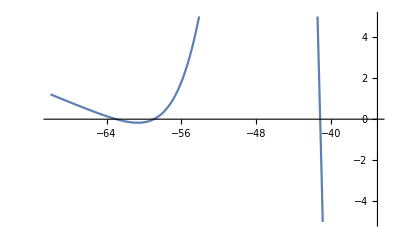

```mathematica
Plot[(-INa-IK-IL-Ipump)/c/.{n->neq,m->meq,h->heq},{v,-70,-39},PlotRange->{{-70,-35},{-5,5}}]
```

```mathematica
(*Equilibrias*)
```

```mathematica
v3=v/.FindRoot[{(-INa-IK-IL-Ipump)/c/.{n->neq,m->meq,h->heq}}==0,{v,-40}][[1]]
```

-41.1242

```mathematica
v1=v/.FindRoot[{(-INa-IK-IL-Ipump)/c/.{n->neq,m->meq,h->heq}}==0,{v,-65}][[1]]
```

-62.9748

```mathematica
(*Eigenvalues of Jacobian for point 1*)
```

```mathematica
dvdv1=D[(-INa-IK-IL-Ipump)/c/.{n->neq/.v->v1,h->heq/.v->v1,m->meq/.v->v1},v]/.{v->v1};
dvdm1=D[(-INa-IK-IL-Ipump)/c/.{n->neq/.v->v1,h->heq/.v->v1},m]/.{v->v1,m->meq/.v->v1};
dvdn1=D[(-INa-IK-IL-Ipump)/c/.{m->meq,h->heq/.v->v1},n]/.{v->v1,n->neq/.v->v1};
dvdh1=D[(-INa-IK-IL-Ipump)/c/.{m->meq,n->neq},h]/.{v->v1,h->heq/.v->v1};
dmdv1=D[(am*(1-m)-bm*m),v]/.{v->v1,m->meq/.v->v1};dndv1=D[(an*(1-n)-bn*n),v]/.{v->v1,n->neq/.v->v1};
dhdv1=D[(ah*(1-h)-bh*h),v]/.{v->v1,h->heq/.v->v1};
dndn1=D[(an*(1-n)-bn*n),n]/.{v->v1,n->neq/.v->v1};
dmdm1=D[(am*(1-m)-bm*m),m]/.{v->v1,m->meq/.v->v1};
dhdh1=D[(ah*(1-h)-bh*h),h]/.{v->v1,h->heq/.v->v1};
```

```mathematica
Eigenvalues[({{dvdv1, dvdm1, dvdn1, dvdh1}, {dmdv1, dmdm1, 0, 0}, {dndv1, 0, dndn1, 0}, {dhdv1, 0, 0, dhdh1}})]
```

{-10.4911,-0.61481,-0.26549,-0.129333}

```mathematica
(*Eigenvalues of Jacobian for point 3*)
```

```mathematica
dvdv3=D[(-INa-IK-IL-Ipump)/c/.{n->neq/.v->v3,h->heq/.v->v3,m->meq/.v->v3},v]/.{v->v3};
dvdm3=D[(-INa-IK-IL-Ipump)/c/.{n->neq/.v->v3,h->heq/.v->v3},m]/.{v->v3,m->meq/.v->v3};
dvdn3=D[(-INa-IK-IL-Ipump)/c/.{m->meq,h->heq/.v->v3},n]/.{v->v3,n->neq/.v->v3};
dvdh3=D[(-INa-IK-IL-Ipump)/c/.{m->meq,n->neq},h]/.{v->v3,h->heq/.v->v3};
dmdv3=D[(am*(1-m)-bm*m),v]/.{v->v3,m->meq/.v->v3};dndv3=D[(an*(1-n)-bn*n),v]/.{v->v3,n->neq/.v->v3};
dhdv3=D[(ah*(1-h)-bh*h),v]/.{v->v3,h->heq/.v->v3};
dndn3=D[(an*(1-n)-bn*n),n]/.{v->v3,n->neq/.v->v3};
dmdm3=D[(am*(1-m)-bm*m),m]/.{v->v3,m->meq/.v->v3};
dhdh3=D[(ah*(1-h)-bh*h),h]/.{v->v3,h->heq/.v->v3};
```

```mathematica
Eigenvalues[({{dvdv3, dvdm3, dvdn3, dvdh3}, {dmdv3, dmdm3, 0, 0}, {dndv3, 0, dndn3, 0}, {dhdv3, 0, 0, dhdh3}})]
```

{-18.0827,4.95533,0.788266,-0.481056}

```mathematica
(*Stability of h around point 3.*)
```

```mathematica
Eigenvalues[({{dvdv3, dvdh3}, {dhdv3, dhdh3}})]
```

{-1.79762+1.72617 ⅈ,-1.79762-1.72617 ⅈ}